# Fractal dimension calculator 2.0

## data processing

## inserire l’immagine come input

```mathematica
img = -Graphics-; temp=img;

(*r=128;{Slider[Dynamic[r],{0,255,1}],Dynamic[r],"r"}
α=0.8;{Slider[Dynamic[α],{-1,1,0.1}],Dynamic[α],"α"}
β=0;{Slider[Dynamic[β],{-1,1,0.1}],Dynamic[β],"β"}
γ=0;{Slider[Dynamic[γ],{-1,1,0.1}],Dynamic[γ],"γ"}
bin = LocalAdaptiveBinarize[img,r,{α,β,γ}];*)
(*r=;α=0.8; β=0; γ=0;*)

Manipulate[LocalAdaptiveBinarize[temp, r,{α, β, γ}],
	{{r, 128}, 1, 255,4, Appearance -> "Labeled"},
	{{α, .8}, -1, 1,0.1, Appearance -> "Labeled"},
	{{β, 0}, -1, 1,0.1, Appearance -> "Labeled"},
	{{γ, 0}, -1, 1,0.1, Appearance -> "Labeled"}]
```

### copia l’immagine sopra qui sotto

```mathematica
temp=-Graphics-;
```

## ridimensionamento immagine

```mathematica
{width,height} = ImageDimensions[temp]
```

{591,1024}

```mathematica
Manipulate[
	Column[{
		bin=ImagePad[temp,{{leftPad,rightPad},{bottomPad,topPad}},White],
		Row[{
			Text@"width e height",
			ImageDimensions@bin
		}," "],
		Row[{
			Text@"Fattori width e height",
			FactorInteger[ImageDimensions[bin]]			
		}," "],
		Row[{
			Text@"possibili dimensioni dei quadretti :",
			seq = Reverse[Intersection @@ Divisors /@ ImageDimensions[bin]] (*!!importantissimo!!*)
		}," "],
		Row[{
			Text@"il numero di pixel neri è : ",
			(*uoh, roba strana *)ImageLevels[ColorConvert[bin, "Grayscale"]][[1, 2]] (*conta pixel neri*)
		}," "]
	}],
	{{leftPad,0},-width,width,1, Appearance->"Labeled"},
	{{rightPad,0},-width,width,1, Appearance->"Labeled"},
	Delimiter,
	{{bottomPad,0},-height,height,1, Appearance->"Labeled"},
	{{topPad,0},-height,height,1, Appearance->"Labeled"},
	ControlPlacement->Left
]
```

## programma vero e proprio

## Boxcount, per difetto e per eccesso

```mathematica
{width,height}=ImageDimensions[bin]

risultatoEccesso = {
  width/#, 
  Last@First@ImageLevels@Image[
      BlockMap[Min, ImageData[bin], {#, #}],
      "Bit"]
  } & /@ seq;

risultatoDifetto = {
  width/#, 
  Last@First@ImageLevels@Image[
      BlockMap[Max, ImageData[bin], {#, #}],
      "Bit"]
  } & /@ seq;
```

{1024,1024}

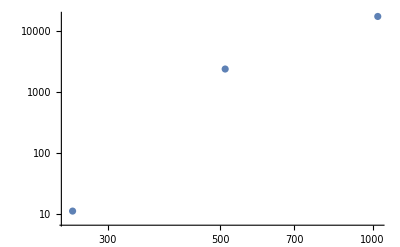

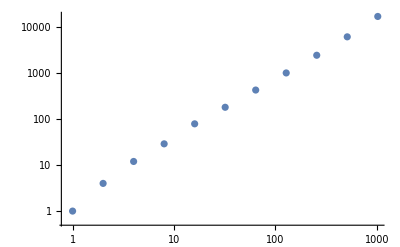

```mathematica
plotD = ListLogLogPlot[risultatoDifetto]
plotE = ListLogLogPlot[risultatoEccesso]
```

## Data Post-Processing

## niente log[0]

```mathematica
risultatoDifetto = Clip[risultatoDifetto,{1,width*height}];
risultatoEccesso = Clip[risultatoEccesso,{1,width*height}];
```

## regressione

```mathematica
fmD = LinearModelFit[Log[risultatoDifetto], {1, x}, x]
fmE = LinearModelFit[Log[risultatoEccesso], {1, x}, x]
```

FittedModel[-2.14364+1.14067 x]

FittedModel[0.422005+1.34877 x]

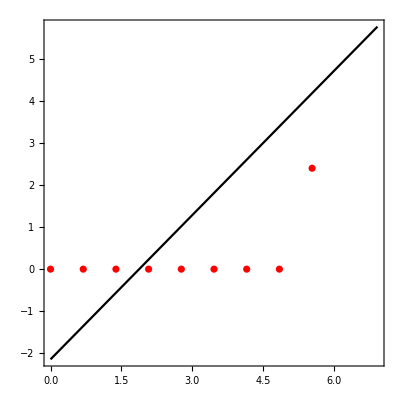

```mathematica
plotD = Show[
  Plot[fmD[x], {x, Log[risultatoDifetto[[1, 1]]], Log[risultatoDifetto[[-1, 1]]]}, 
   PlotStyle -> Black],
  ListLogLogPlot[risultatoDifetto, PlotStyle -> Red],
  AspectRatio -> 1, Axes -> False, Frame -> True
]
```

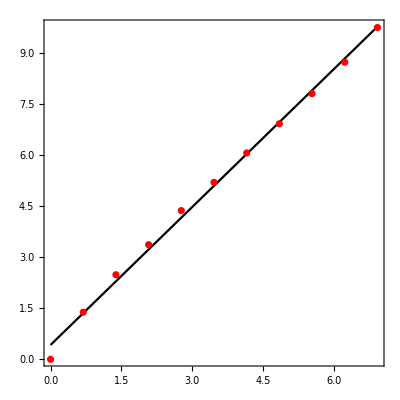

```mathematica
plotE = Show[
  Plot[fmE[x], {x, Log[risultatoEccesso[[1, 1]]], Log[risultatoEccesso[[-1, 1]]]}, 
   PlotStyle -> Black],
  ListLogLogPlot[risultatoEccesso, PlotStyle -> Red],
  AspectRatio -> 1, Axes -> False, Frame -> True
]
```

## Elaborazione risultato con animazione

```mathematica
imgsD = Image[BlockMap[Max, ImageData[bin], {#, #}], "Bit"] & /@ seq;
imgsE = Image[BlockMap[Min, ImageData[bin], {#, #}], "Bit"] & /@ seq;
```

```mathematica
sz = 200;

imgsD = If[First@ImageDimensions[#] > sz, 
     ImageResize[Image[#, Real], sz], 
     ImageResize[#, sz, Resampling -> "Nearest"]] & /@ imgsD;

imgsE = If[First@ImageDimensions[#] > sz, 
     ImageResize[Image[#, Real], sz], 
     ImageResize[#, sz, Resampling -> "Nearest"]] & /@ imgsE;

frmD = Table[
  ImageCompose[ImageResize[bin, sz], {im, 0.5}], {im, imgsD}];
  
frmE = Table[
  ImageCompose[ImageResize[bin, sz], {im, 0.5}], {im, imgsE}];

Column[{
Row[{ListAnimate[imgsD],ListAnimate[imgsE]}] ,
Row[{ListAnimate[frmD],ListAnimate[frmE]}] 
}]
```

```mathematica
framesD = Table[
   Row[{
     Show[plotD, ImageSize -> 300, 
      Epilog -> {AbsolutePointSize[10], Red, Point@Log[risultatoDifetto[[i]]]}],
      Image[frmD[[i]], Magnification -> 1]
     }],
   {i, Length[imgsD]}];
   
framesE = Table[
   Row[{
     Show[plotE, ImageSize -> 300, 
      Epilog -> {AbsolutePointSize[10], Red, Point@Log[risultatoEccesso[[i]]]}],
      Image[frmE[[i]], Magnification -> 1]
     }],
   {i, Length[imgsE]}];

Row[{ListAnimate[framesD],ListAnimate[framesE]}]
```

```mathematica
risultatoDifetto[[-2]]//MatrixForm
risultatoEccesso[[-2]]//MatrixForm (*uoh, giusto sono uguali*)
eps=1024;
n=17090;
N @ (Log[n]/Log[1/eps])
```

(106
28)

(106
1267)

-1.40609

```mathematica
Expand@Mean[{fmE,fmD}]
```

FittedModel[-2.14364+1.14067 x]/2+FittedModel[0.422005+1.34877 x]/2

```mathematica
(1.140672206643438+1.3487684826540938)*1/2
```

1.24472